## 5 sites

## Stationary points and their positions

### General declaration

```mathematica
hamiltonian[j_,u_,p1_,p2_,p3_,p4_,q1_,q2_,q3_,q4_]:=-j((q1+q4)√(2  - q1^2-q2^2-q3^2-q4^2-p1^2-p2^2-p3^2-p4^2) + q1 q2 + p1 p2 +  q2 q3 + p2 p3+q3 q4+p3 p4 ) + u/4((2  - q1^2-q2^2-q3^2-q4^2-p1^2-p2^2-p3^2-p4^2)^2 + (q1^2+p1^2)^2+(q2^2+p2^2)^2+(q3^2+p3^2)^2+(q4^2+p4^2)^2)
```

```mathematica
stepj=1/500;j0=1/10000;u0=1/10000;stepu=1/10;
```

```mathematica
SetOptions[ListPlot,BaseStyle->{FontFamily->"Arial",FontSize->20,PointSize->0.002,GridLinesStyle->Thick},ImageSize->800,AxesStyle->Thick];
```

### Special points

```mathematica
u=u0+1
```

10001/10000

#### Inicialisation

```mathematica
q1d=FullSimplify[D[hamiltonian[j,u,p1,p2,p3,p4,q1,q2,q3,q4],p1]];
q2d=FullSimplify[D[hamiltonian[j,u,p1,p2,p3,p4,q1,q2,q3,q4],p2]];
q3d=FullSimplify[D[hamiltonian[j,u,p1,p2,p3,p4,q1,q2,q3,q4],p3]];
q4d=FullSimplify[D[hamiltonian[j,u,p1,p2,p3,p4,q1,q2,q3,q4],p4]];
p1d=FullSimplify[D[hamiltonian[j,u,p1,p2,p3,p4,q1,q2,q3,q4],q1]];
p2d=FullSimplify[D[hamiltonian[j,u,p1,p2,p3,p4,q1,q2,q3,q4],q2]];
p3d=FullSimplify[D[hamiltonian[j,u,p1,p2,p3,p4,q1,q2,q3,q4],q3]];p4d=FullSimplify[D[hamiltonian[j,u,p1,p2,p3,p4,q1,q2,q3,q4],q4]];
```

#### Parallel calculation

```mathematica
LaunchKernels[12];
```

```mathematica
result=ParallelTable[Module[{s,t},t=Timing[TimeConstrained[s=Quiet[NSolve[{q1d==0,q2d==0,q3d=0,q4d==0,p1d==0,p2d==0,p3d==0p4d==0},{q1,p1,q2,p2,q3,p3,q4,p4},Reals,WorkingPrecision->100]],3600]][[1]];{
j,t,Length[s],
If[Length[s]>0,
{Tuples[{{j},hamiltonian[j,u,p1,p2,p3,p4,q1,q2,q3,q4]/.s}],
Tuples[{{j},q1/.s}],
Tuples[{{j},q2/.s}],
Tuples[{{j},q3/.s}],
Tuples[{{j},q4/.s}],
Tuples[{{j},p1/.s}],
Tuples[{{j},p2/.s}],
Tuples[{{j},p3/.s}],
Tuples[{{j},p4/.s}]},{}]}],{j,j0,2,20stepj},Method->"FinestGrained"];
```

#### Reordering

```mathematica
tq1={};
tq2={};
tq3={};
tq4={};
tp1={};
tp2={};
tp3={};
tp4={};
```

```mathematica
h={};
t={};
n={};
```

```mathematica
Do[t=Join[t, {item[[1]],item[[2]]}];
n=Join[n,{item[[1]],item[[3]]}];
If[item[[3]]>0,
h=Join[h,item[[4]][[1]]];

tq1=Join[h,item[[4]][[2]]];
tq2=Join[h,item[[4]][[3]]];
tq3=Join[h,item[[4]][[4]]];
tq4=Join[h,item[[4]][[5]]];
tp1=Join[h,item[[4]][[6]]];
tp2=Join[h,item[[4]][[7]]];
tp3=Join[h,item[[4]][[8]]];
tp4=Join[h,item[[4]][[9]]]],{item,result}]
```

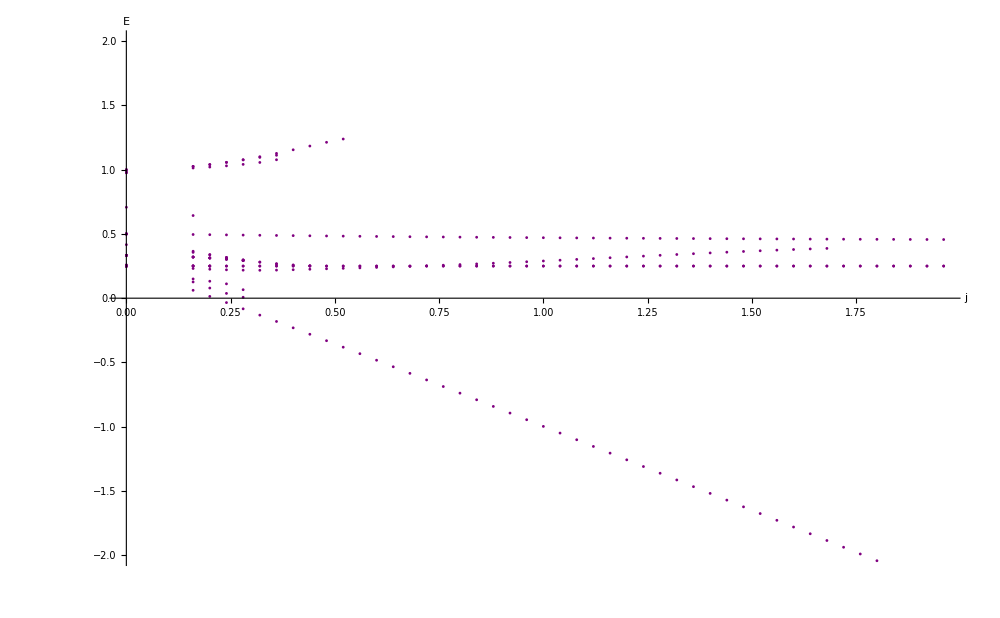

```mathematica
ListPlot[h,PlotRange->{-2,2},PlotStyle->Purple,AxesLabel->{"j","E"}]
```

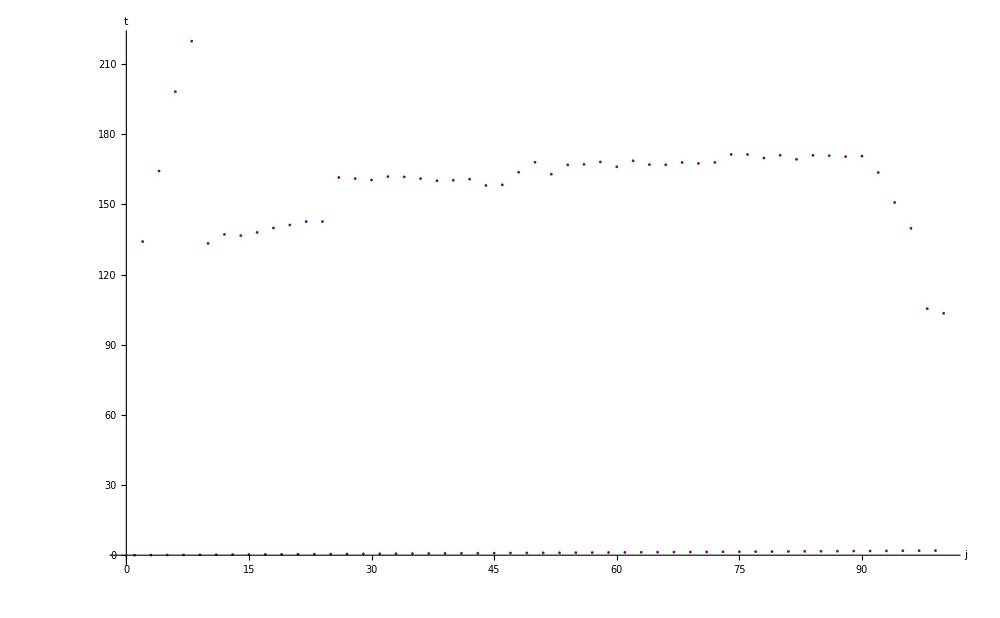

```mathematica
ListPlot[t,PlotStyle->Purple,AxesLabel->{"j","t"}]
```

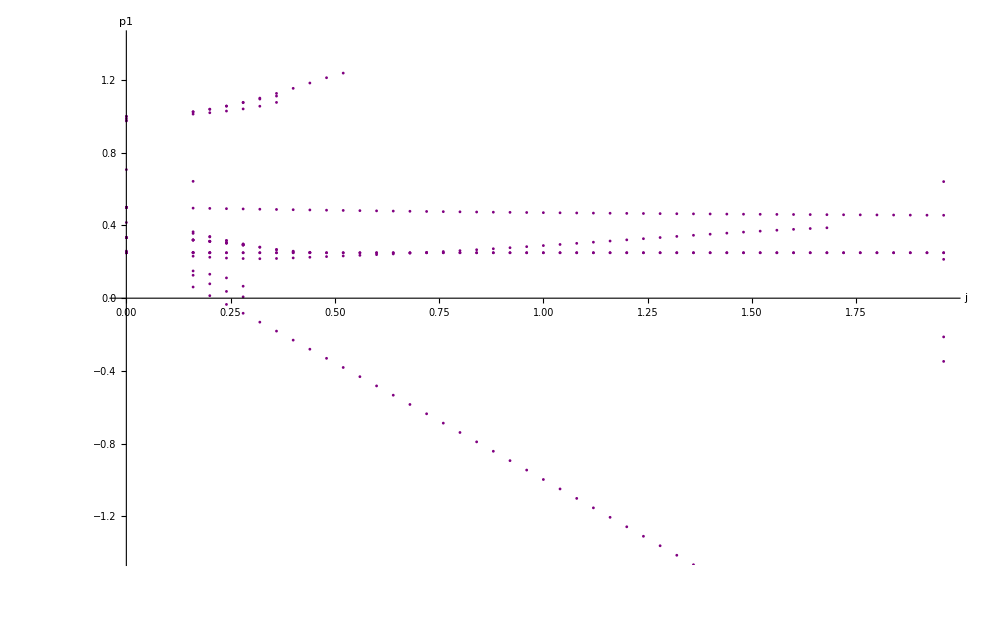

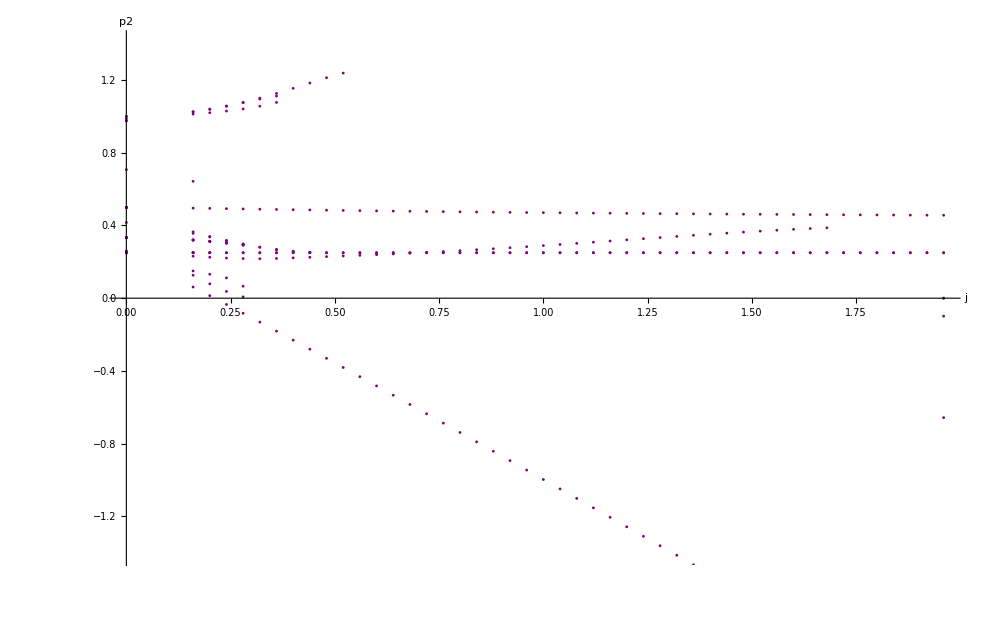

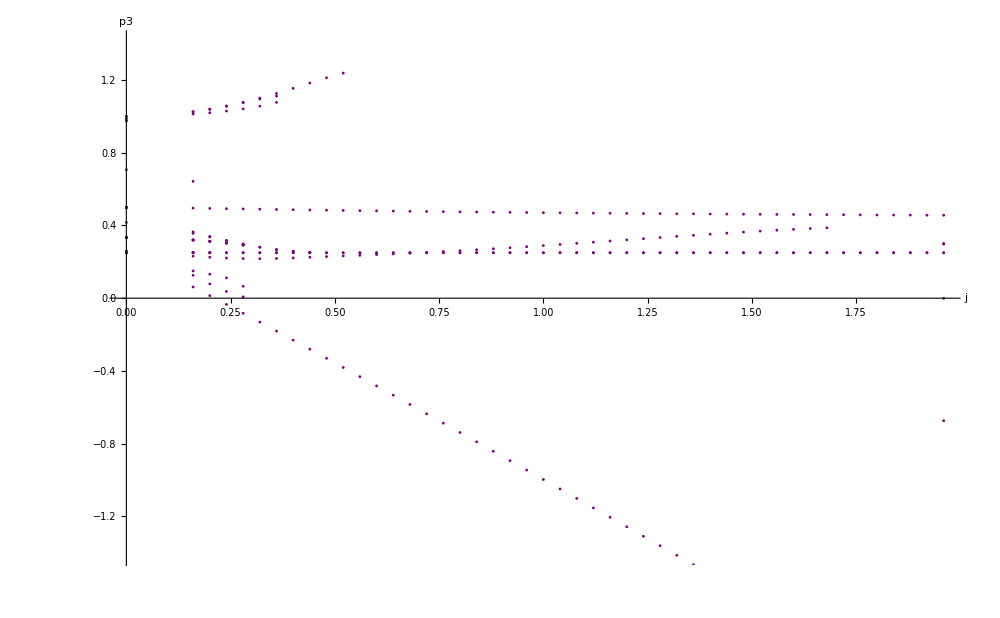

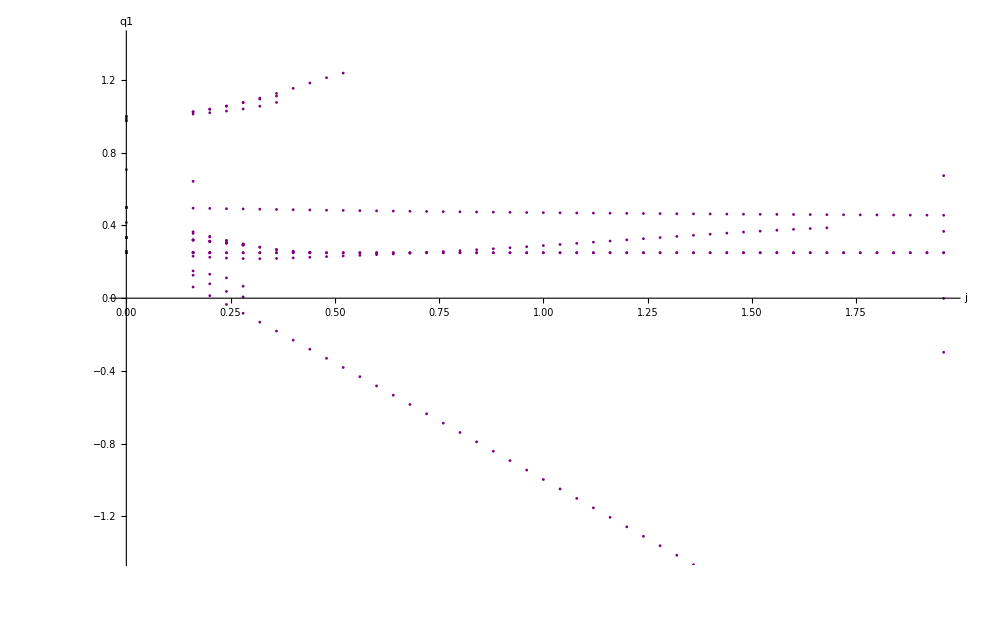

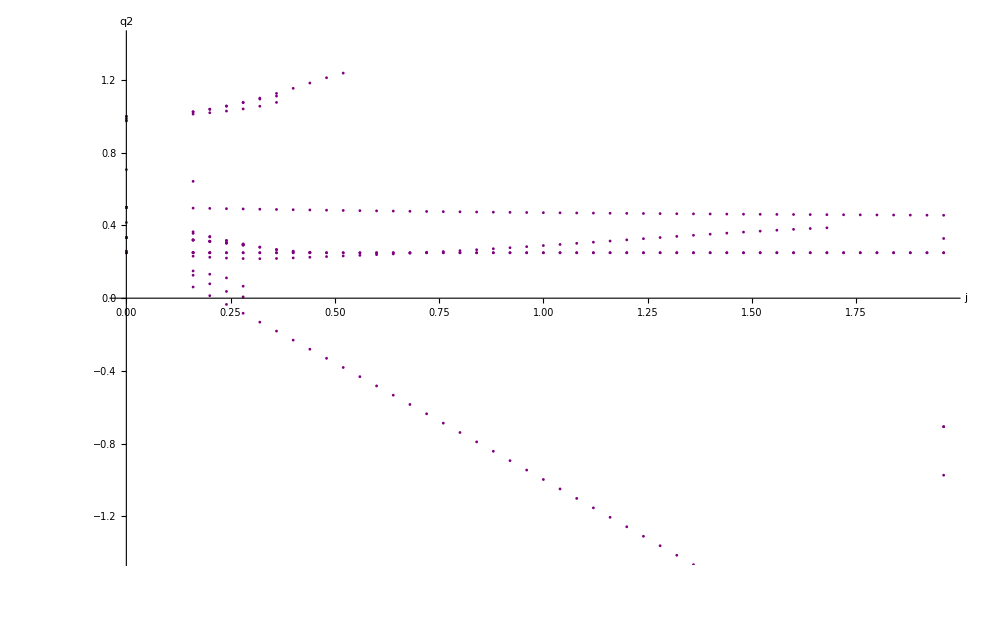

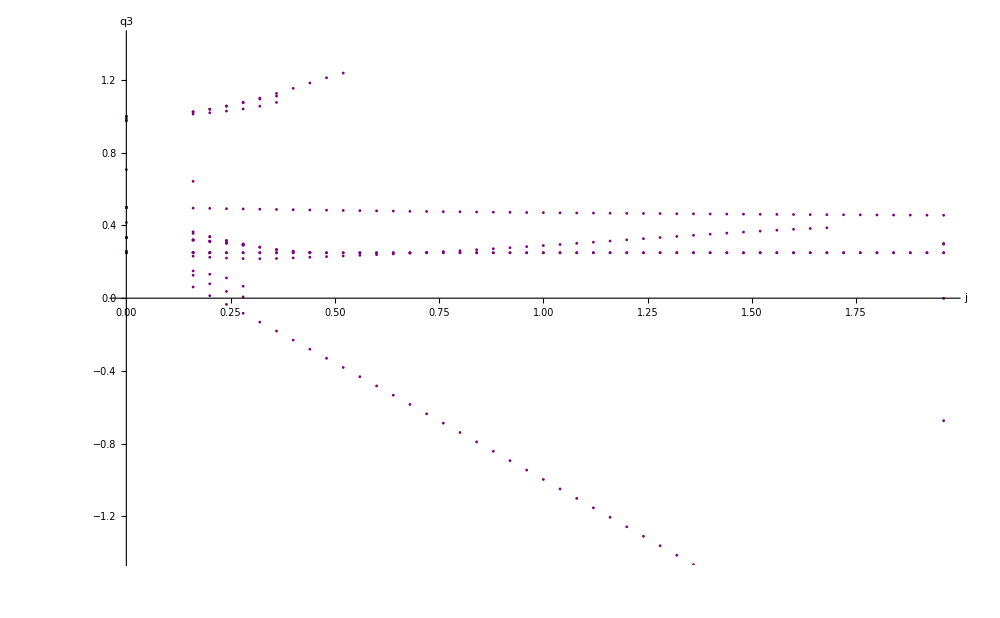

```mathematica
ListPlot[tp1,PlotRange->{-√2,√2},PlotStyle->Purple,AxesLabel->{"j","p1"}]
ListPlot[tp2,PlotRange->{-√2,√2},PlotStyle->Purple,AxesLabel->{"j","p2"}]
ListPlot[tp3,PlotRange->{-√2,√2},PlotStyle->Purple,AxesLabel->{"j","p3"}]
ListPlot[tq1,PlotRange->{-√2,√2},PlotStyle->Purple,AxesLabel->{"j","q1"}]
ListPlot[tq2,PlotRange->{-√2,√2},PlotStyle->Purple,AxesLabel->{"j","q2"}]
ListPlot[tq3,PlotRange->{-√2,√2},PlotStyle->Purple,AxesLabel->{"j","q3"}]
```

#### Saving

```mathematica
Export["d:\\h.txt",N[h],"CSV"];
Export["d:\\n.txt",N[n],"CSV"];
Export["d:\\t.txt",N[t],"CSV"];
Export["d:\\tq1.txt",N[tq1],"CSV"];
Export["d:\\tq2.txt",N[tq2],"CSV"];
Export["d:\\tq3.txt",N[tq3],"CSV"];
Export["d:\\tp1.txt",N[tp1],"CSV"];
Export["d:\\tp2.txt",N[tp2],"CSV"];
Export["d:\\tp3.txt",N[tp3],"CSV"];
```

## 4 sites

## Stationary points and their positions

### General declaration

```mathematica
hamiltonian[j_,u_,p1_,p2_,p3_,q1_,q2_,q3_]:=-j((q1+q3)√(2  - q1^2-q2^2-q3^2-p1^2-p2^2-p3^2) + q1 q2 + p1 p2 +  q2 q3 + p2 p3 ) + u/4((2  - q1^2-q2^2-q3^2-p1^2-p2^2-p3^2)^2 + (q1^2+p1^2)^2+(q2^2+p2^2)^2+(q3^2+p3^2)^2)
```

```mathematica
stepj=1/1000;j0=1/11111;u0=1/10000;stepu=1/10;
```

```mathematica
SetOptions[ListPlot,BaseStyle->{FontFamily->"Arial",FontSize->20,PointSize->0.002,GridLinesStyle->Thick},ImageSize->800,AxesStyle->Thick];
```

### Special points

```mathematica
u=u0+1
```

10001/10000

#### Inicialisation

```mathematica
u=-5;
stepj=0.001;
j0=stepj;
```

```mathematica
q1d=FullSimplify[D[hamiltonian[j,u,p1,p2,p3,q1,q2,q3],p1]]
q2d=FullSimplify[D[hamiltonian[j,u,p1,p2,p3,q1,q2,q3],p2]]
q3d=FullSimplify[D[hamiltonian[j,u,p1,p2,p3,q1,q2,q3],p3]]
p1d=FullSimplify[D[hamiltonian[j,u,p1,p2,p3,q1,q2,q3],q1]]
p2d=FullSimplify[D[hamiltonian[j,u,p1,p2,p3,q1,q2,q3],q2]]
p3d=FullSimplify[D[hamiltonian[j,u,p1,p2,p3,q1,q2,q3],q3]]
```

-j p2-5 p1 (p1^2+q1^2)+(j p1 (q1+q3))/(√(2-p1^2-p2^2-p3^2-q1^2-q2^2-q3^2))-5 p1 (-2+p1^2+p2^2+p3^2+q1^2+q2^2+q3^2)

-j (p1+p3)+(j p2 (q1+q3))/(√(2-p1^2-p2^2-p3^2-q1^2-q2^2-q3^2))-5 p2 (-2+p1^2+2 p2^2+p3^2+q1^2+2 q2^2+q3^2)

-j p2+(j p3 (q1+q3))/(√(2-p1^2-p2^2-p3^2-q1^2-q2^2-q3^2))-5 p3 (-2+p1^2+p2^2+2 p3^2+q1^2+q2^2+2 q3^2)

-5 q1 (p1^2+q1^2)-j q2+(j q1 (q1+q3))/(√(2-p1^2-p2^2-p3^2-q1^2-q2^2-q3^2))-j √(2-p1^2-p2^2-p3^2-q1^2-q2^2-q3^2)-5 q1 (-2+p1^2+p2^2+p3^2+q1^2+q2^2+q3^2)

-j q1-5 q2 (p2^2+q2^2)-j q3+(j q2 (q1+q3))/(√(2-p1^2-p2^2-p3^2-q1^2-q2^2-q3^2))-5 q2 (-2+p1^2+p2^2+p3^2+q1^2+q2^2+q3^2)

-j q2+(j q3 (q1+q3))/(√(2-p1^2-p2^2-p3^2-q1^2-q2^2-q3^2))-j √(2-p1^2-p2^2-p3^2-q1^2-q2^2-q3^2)-5 q3 (p3^2+q3^2)-5 q3 (-2+p1^2+p2^2+p3^2+q1^2+q2^2+q3^2)

#### Special value

```mathematica
j=1
```

1

```mathematica
eqns={q1d==0,q2d==0,q3d==0,p1d==0,p2d==0,p3d==0}
vars={p1,p2,p3,q1,q2,q3}
check={q1d,q2d,q3d,p1d,p2d,p3d}
```

{-j p2-5 p1 (p1^2+q1^2)+(j p1 (q1+q3))/(√(2-p1^2-p2^2-p3^2-q1^2-q2^2-q3^2))-5 p1 (-2+p1^2+p2^2+p3^2+q1^2+q2^2+q3^2)==0,-j (p1+p3)+(j p2 (q1+q3))/(√(2-p1^2-p2^2-p3^2-q1^2-q2^2-q3^2))-5 p2 (-2+p1^2+2 p2^2+p3^2+q1^2+2 q2^2+q3^2)==0,-j p2+(j p3 (q1+q3))/(√(2-p1^2-p2^2-p3^2-q1^2-q2^2-q3^2))-5 p3 (-2+p1^2+p2^2+2 p3^2+q1^2+q2^2+2 q3^2)==0,-5 q1 (p1^2+q1^2)-j q2+(j q1 (q1+q3))/(√(2-p1^2-p2^2-p3^2-q1^2-q2^2-q3^2))-j √(2-p1^2-p2^2-p3^2-q1^2-q2^2-q3^2)-5 q1 (-2+p1^2+p2^2+p3^2+q1^2+q2^2+q3^2)==0,-j q1-5 q2 (p2^2+q2^2)-j q3+(j q2 (q1+q3))/(√(2-p1^2-p2^2-p3^2-q1^2-q2^2-q3^2))-5 q2 (-2+p1^2+p2^2+p3^2+q1^2+q2^2+q3^2)==0,-j q2+(j q3 (q1+q3))/(√(2-p1^2-p2^2-p3^2-q1^2-q2^2-q3^2))-j √(2-p1^2-p2^2-p3^2-q1^2-q2^2-q3^2)-5 q3 (p3^2+q3^2)-5 q3 (-2+p1^2+p2^2+p3^2+q1^2+q2^2+q3^2)==0}

{p1,p2,p3,q1,q2,q3}

{-j p2-5 p1 (p1^2+q1^2)+(j p1 (q1+q3))/(√(2-p1^2-p2^2-p3^2-q1^2-q2^2-q3^2))-5 p1 (-2+p1^2+p2^2+p3^2+q1^2+q2^2+q3^2),-j (p1+p3)+(j p2 (q1+q3))/(√(2-p1^2-p2^2-p3^2-q1^2-q2^2-q3^2))-5 p2 (-2+p1^2+2 p2^2+p3^2+q1^2+2 q2^2+q3^2),-j p2+(j p3 (q1+q3))/(√(2-p1^2-p2^2-p3^2-q1^2-q2^2-q3^2))-5 p3 (-2+p1^2+p2^2+2 p3^2+q1^2+q2^2+2 q3^2),-5 q1 (p1^2+q1^2)-j q2+(j q1 (q1+q3))/(√(2-p1^2-p2^2-p3^2-q1^2-q2^2-q3^2))-j √(2-p1^2-p2^2-p3^2-q1^2-q2^2-q3^2)-5 q1 (-2+p1^2+p2^2+p3^2+q1^2+q2^2+q3^2),-j q1-5 q2 (p2^2+q2^2)-j q3+(j q2 (q1+q3))/(√(2-p1^2-p2^2-p3^2-q1^2-q2^2-q3^2))-5 q2 (-2+p1^2+p2^2+p3^2+q1^2+q2^2+q3^2),-j q2+(j q3 (q1+q3))/(√(2-p1^2-p2^2-p3^2-q1^2-q2^2-q3^2))-j √(2-p1^2-p2^2-p3^2-q1^2-q2^2-q3^2)-5 q3 (p3^2+q3^2)-5 q3 (-2+p1^2+p2^2+p3^2+q1^2+q2^2+q3^2)}

```mathematica
solutions=Module[{guess,result},
result={};
Do[guess=RandomReal[{-√2,√2},6];
If[guess.guess<2,Quiet[sol=Chop[FindRoot[eqns,Transpose[{vars, guess}]]]];
If[Total[Abs[check]/.sol]<10^-4&&Total[Abs[Im[check]]/.sol]==0,
result=Append[result,sol]]],{i,1,1000} ];result=Union[result,SameTest->(Norm[Values[#1]-Values[#2]]<10^-4&)];result]
```

```mathematica
LaunchKernels[12];
```

```mathematica
result=ParallelTable[Module[{guess,result,t,sol},
result={};
t=Timing[Do[guess=RandomReal[{-√2,√2},6];
If[guess.guess<2,Quiet[sol=Chop[FindRoot[eqns,Transpose[{vars, guess}]]]];
If[Total[Abs[check]/.sol]<10^-4&&Total[Abs[Im[check]]/.sol]==0,
result=Append[result,sol]]],{i,1,1000} ];result=Union[result,SameTest->(Norm[Values[#1]-Values[#2]]<10^-4&)]][[1]];{
j,t,Length[result],
If[Length[result]>0,
{Tuples[{{j},hamiltonian[j,u,p1,p2,p3,q1,q2,q3]/.result}],
Tuples[{{j},q1/.result}],
Tuples[{{j},q2/.result}],
Tuples[{{j},q3/.result}],
Tuples[{{j},p1/.result}],
Tuples[{{j},p2/.result}],
Tuples[{{j},p3/.result}],
Tuples[{{j},(p1^2+q1^2)/.result}],
Tuples[{{j},(p2^2+q2^2)/.result}],
Tuples[{{j},(p3^2+q3^2)/.result}]
},{}]}],{j,-2,2,20stepj},Method->"FinestGrained"];
```

#### Parallel calculation

```mathematica
LaunchKernels[12];
```

```mathematica
result=ParallelTable[Module[{s,t},t=Timing[s=Quiet[NSolve[{q1d==0,q2d==0,q3d=0,p1d==0,p2d==0,p3d==0},{q1,q2,q3,p1,p2,p3},Reals,WorkingPrecision->100]]][[1]];{
j,t,Length[s],
If[Length[s]>0,
{Tuples[{{j},hamiltonian[j,u,p1,p2,p3,q1,q2,q3]/.s}],
Tuples[{{j},q1/.s}],
Tuples[{{j},q2/.s}],
Tuples[{{j},q3/.s}],
Tuples[{{j},p1/.s}],
Tuples[{{j},p2/.s}],
Tuples[{{j},p3/.s}],
Tuples[{{j},(p1^2+q1^2)/.s}],
Tuples[{{j},(p2^2+q2^2)/.s}],
Tuples[{{j},(p3^2+q3^2)/.s}]
},{}]}],{j,-2,2,20stepj},Method->"FinestGrained"];
```

#### Reordering

```mathematica
tq1={};
tq2={};
tq3={};
tp1={};
tp2={};
tp3={};

h={};
t={};
n={};
```

```mathematica
Do[t=Join[t, {{item[[1]],item[[2]]}}];
n=Join[n,{{item[[1]],item[[3]]}}];
If[item[[3]]>0,
h=Join[h,item[[4]][[1]]];
tq1=Join[tq1,item[[4]][[2]]];
tq2=Join[tq2,item[[4]][[3]]];
tq3=Join[tq3,item[[4]][[4]]];
tp1=Join[tp1,item[[4]][[5]]];
tp2=Join[tp2,item[[4]][[6]]];
tp3=Join[tp3,item[[4]][[7]]]],{item,result}]
```

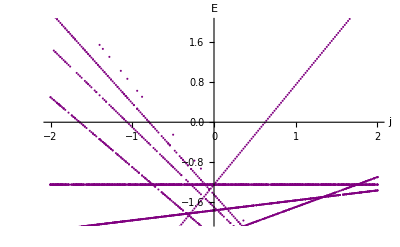

```mathematica
ListPlot[h,PlotRange->{-2,2},PlotStyle->Purple,AxesLabel->{"j","E"}]
```

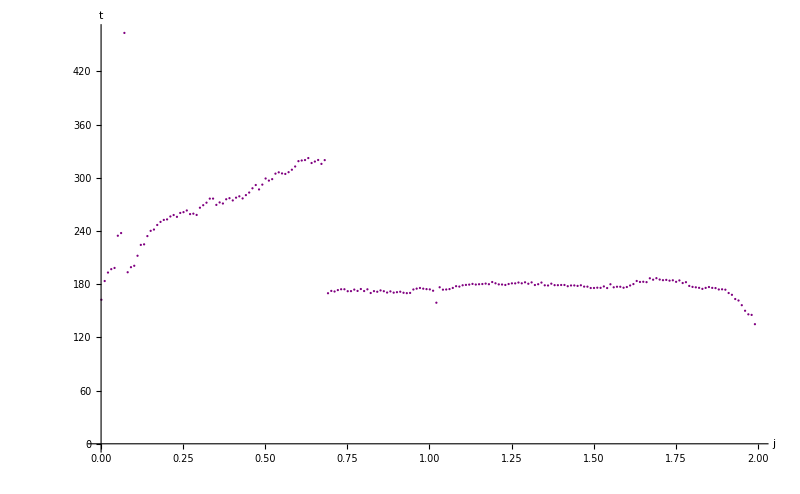

```mathematica
ListPlot[t,PlotStyle->Purple,AxesLabel->{"j","t"}]
```

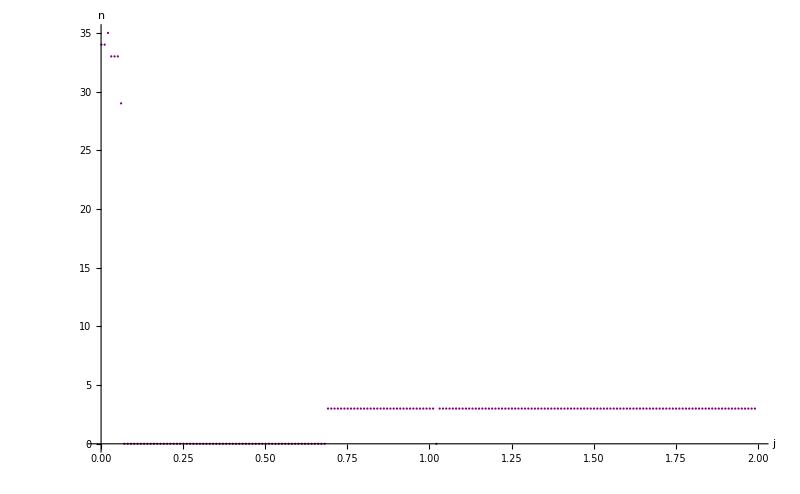

```mathematica
ListPlot[n,PlotStyle->Purple,AxesLabel->{"j","n"},PlotRange->All]
```

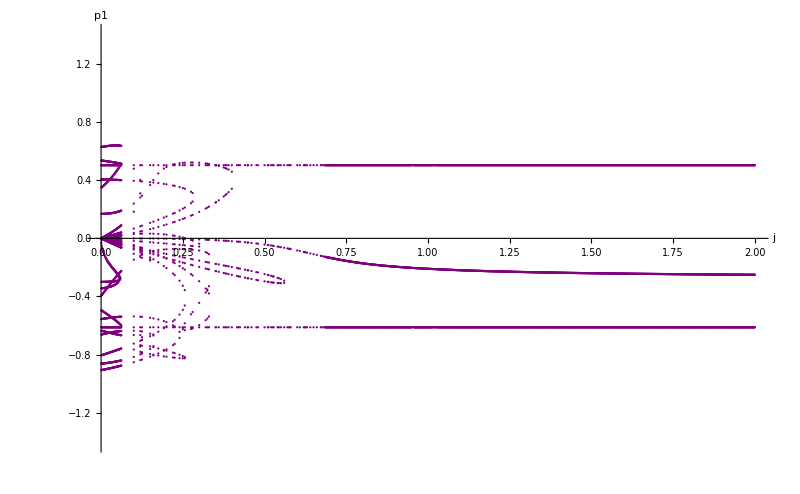

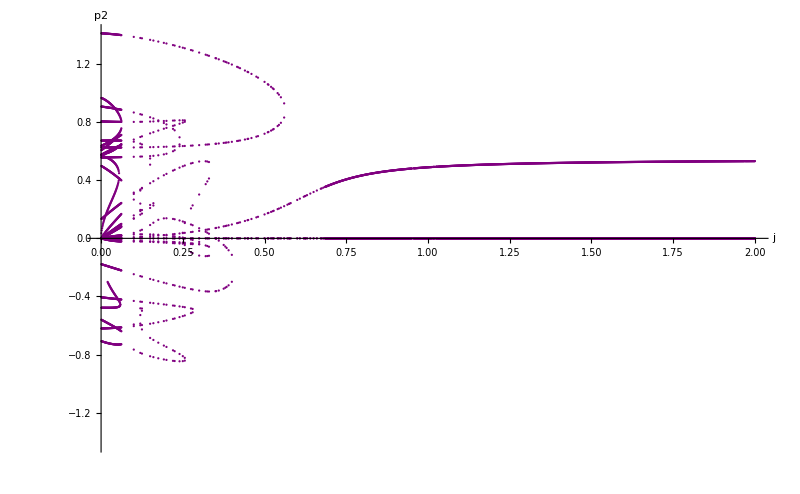

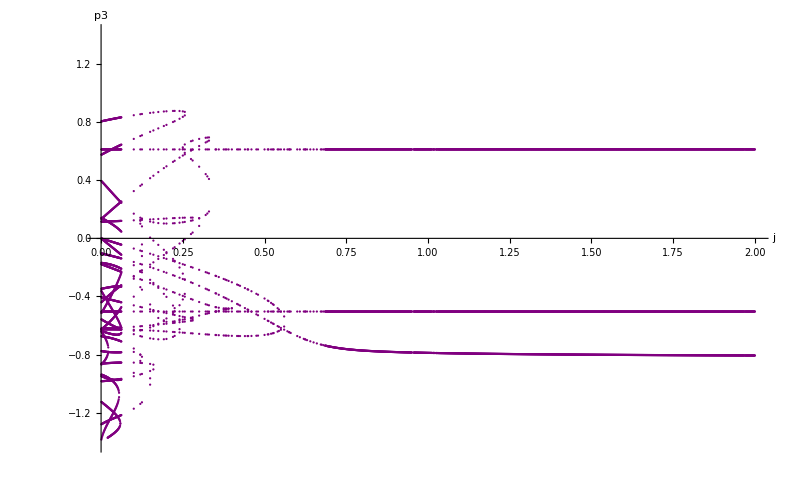

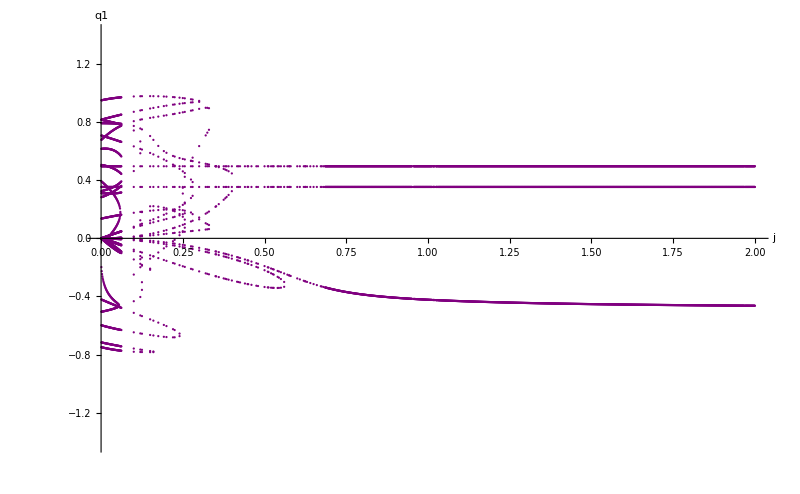

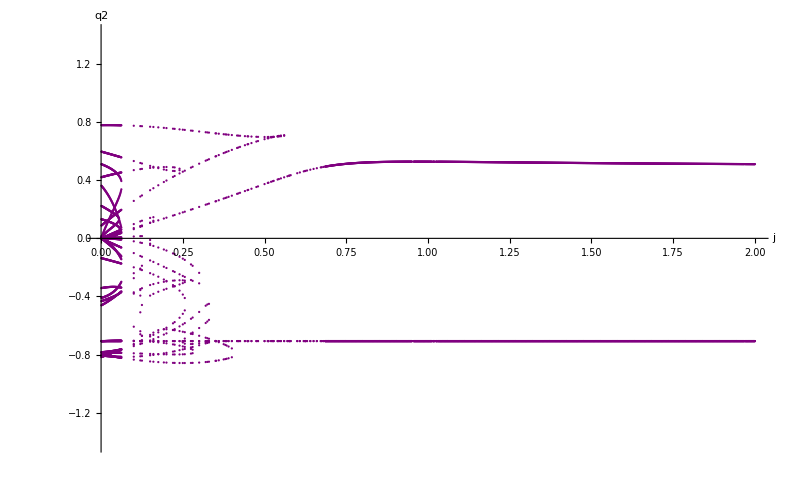

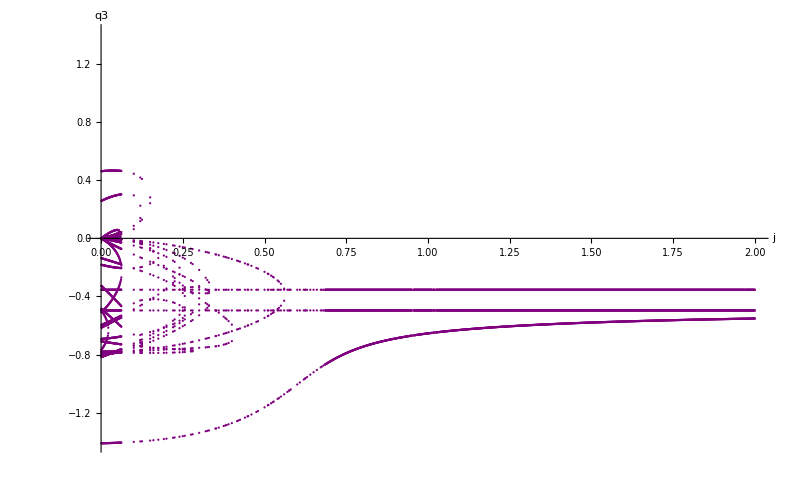

```mathematica
ListPlot[tp1,PlotRange->{-√2,√2},PlotStyle->Purple,AxesLabel->{"j","p1"}]
ListPlot[tp2,PlotRange->{-√2,√2},PlotStyle->Purple,AxesLabel->{"j","p2"}]
ListPlot[tp3,PlotRange->{-√2,√2},PlotStyle->Purple,AxesLabel->{"j","p3"}]
ListPlot[tq1,PlotRange->{-√2,√2},PlotStyle->Purple,AxesLabel->{"j","q1"}]
ListPlot[tq2,PlotRange->{-√2,√2},PlotStyle->Purple,AxesLabel->{"j","q2"}]
ListPlot[tq3,PlotRange->{-√2,√2},PlotStyle->Purple,AxesLabel->{"j","q3"}]
```

#### Saving

```mathematica
Export["d:\\h.txt",N[h],"CSV"];
Export["d:\\n.txt",N[n],"CSV"];
Export["d:\\t.txt",N[t],"CSV"];
Export["d:\\tq1.txt",N[tq1],"CSV"];
Export["d:\\tq2.txt",N[tq2],"CSV"];
Export["d:\\tq3.txt",N[tq3],"CSV"];
Export["d:\\tp1.txt",N[tp1],"CSV"];
Export["d:\\tp2.txt",N[tp2],"CSV"];
Export["d:\\tp3.txt",N[tp3],"CSV"];
```

### One-thread calculation

```mathematica
tq1={};
tq2={};
tq3={};
tp1={};
tp2={};
tp3={};

h={};
i={};
l={};
```

```mathematica
Monitor[For[j=j0,j≤2,j+=stepj,
t=Timing[TimeConstrained[s=Quiet[NSolve[{q1d==0,q2d==0,q3d=0,p1d==0,p2d==0,p3d==0},{q1,p1,q2,p2,q3,p3},Reals,WorkingPrecision->100]];
If[Length[s]>0,
h=Join[h,Tuples[{{j},hamiltonian[j,uu,p1,p2,p3,q1,q2,q3]/.s}]];
(*i=Join[i,Tuples[{{jj},(Total[Sign[Eigenvalues[#]]]/3-3)&/@(hessian[uu,jj]/.s)}]];*)
l=Join[l,{{ll,Length[s]}}];
tq1=Join[tq1,Tuples[{{j},q1/.s}]];
tq2=Join[tq2,Tuples[{{j},q2/.s}]];
tq3=Join[tq3,Tuples[{{j},q3/.s}]];
tp1=Join[tp1,Tuples[{{j},p1/.s}]];
tp2=Join[tp2,Tuples[{{j},p2/.s}]];
tp3=Join[tp3,Tuples[{{j},p3/.s}]]],300]][[1]]],{(j-j0)//N,t}];
```

$Aborted

### Full calculation

```mathematica
Monitor[For[c=c0,c≤1+c0,c+=stepc,
tx={};
ty={};
tpx={};
tpy={};
h={};
i={};
l={};
xd=FullSimplify[D[hamiltonian[AA,BB,c,px,py,x,y],px]];
yd=FullSimplify[D[hamiltonian[AA,BB,c,px,py,x,y],py]];
pxd=FullSimplify[D[hamiltonian[AA,BB,c,px,py,x,y],x]];
pyd=FullSimplify[D[hamiltonian[AA,BB,c,px,py,x,y],y]];
For[a=a0,a≤1,a+=stepa,
t=Timing[TimeConstrained[s=Quiet[Check[NSolve[{xd==0,yd==0,pxd==0,pyd==0}/.{AA->(1-a)/2,BB->-a},{x,px,y,py},Reals,WorkingPrecision->100],{}]];
If[Length[s]>0,
h=Join[h,Tuples[{{a},hamiltonian[(1-a)/2,-a,c,px,py,x,y]/.s}]];
i=Join[i,Tuples[{{a},(Total[Sign[Eigenvalues[#]]]/2-2)&/@(hessian[(1-a)/2,-a,c]/.s)}]];
l=Join[l,{{a,Length[s]}}];
tx=Join[tx,Tuples[{{a},x/.s}]];
ty=Join[ty,Tuples[{{a},y/.s}]];
tpx=Join[tpx,Tuples[{{a},px/.s}]];
tpy=Join[tpy,Tuples[{{a},py/.s}]]],60]][[1]]];
Export["D:\\results\\Vibron\\x" <> ToString[(c-c0)/stepc] <> ".png",ListPlot[tx,PlotRange->{-√2,√2},PlotStyle->Brown,PlotLabel->"C="<>ToString[N[c-c0,3]],AxesLabel->{"ξ","x"}]];
Export["D:\\results\\Vibron\\y" <> ToString[(c-c0)/stepc] <> ".png",ListPlot[ty,PlotRange->{-√2,√2},PlotLabel->"C="<>ToString[N[c-c0,3]],AxesLabel->{"ξ","y"}]];
Export["D:\\results\\Vibron\\px" <> ToString[(c-c0)/stepc] <> ".png",ListPlot[tpx,PlotRange->{-√2,√2},PlotStyle->Brown,PlotLabel->"C="<>ToString[N[c-c0,3]],AxesLabel->{"ξ","px"}]];
Export["D:\\results\\Vibron\\py" <> ToString[(c-c0)/stepc] <> ".png",ListPlot[tpy,PlotRange->{-√2,√2},PlotLabel->"C="<>ToString[N[c-c0,3]],AxesLabel->{"ξ","py"}]];
Export["D:\\results\\Vibron\\h" <> ToString[(c-c0)/stepc] <> ".png",ListPlot[h,PlotRange->{-2,2},PlotStyle->Purple,PlotLabel->"C="<>ToString[N[c-c0,3]],AxesLabel->{"ξ","E"}]]],{(a-a0)//N,(c-c0)//N,t}]
```

## 3 sites

## Stationary points and their positions

### General declaration

```mathematica
hamiltonian[j_,u_,p1_,p2_,q1_,q2_]:=-j((q1+q2)√(2  - q1^2-q2^2-p1^2-p2^2) + q1 q2 + p1 p2 ) + u/4((2  - q1^2-q2^2-p1^2-p2^2)^2 + (q1^2+p1^2)^2+(q2^2+p2^2)^2)
```

```mathematica
stepj=1/1000;j0=1/10000;u0=1/10000;stepu=1/10;
```

```mathematica
SetOptions[ListPlot,BaseStyle->{FontFamily->"Arial",FontSize->20,PointSize->0.002,GridLinesStyle->Thick},ImageSize->800,AxesStyle->Thick];
```

### Special points

```mathematica
u=u0+1
```

10001/10000

#### Inicialisation

```mathematica
u=1;
stepj=0.001;
j0=stepj;
```

```mathematica
q1d=FullSimplify[D[hamiltonian[j,u,p1,p2,q1,q2],p1]]
q2d=FullSimplify[D[hamiltonian[j,u,p1,p2,q1,q2],p2]]
p1d=FullSimplify[D[hamiltonian[j,u,p1,p2,q1,q2],q1]]
p2d=FullSimplify[D[hamiltonian[j,u,p1,p2,q1,q2],q2]]
```

2 p1^3-j p2+p1 (-2+p2^2+2 q1^2+q2^2+(j (q1+q2))/(√(2-p1^2-p2^2-q1^2-q2^2)))

-j p1+(j p2 (q1+q2))/(√(2-p1^2-p2^2-q1^2-q2^2))+p2 (-2+p1^2+2 p2^2+q1^2+2 q2^2)

-j q2+q1 (-2+2 p1^2+p2^2+2 q1^2+q2^2)+(j (-2+p1^2+p2^2+2 q1^2+q1 q2+q2^2))/(√(2-p1^2-p2^2-q1^2-q2^2))

q2 (p2^2+q2^2)+q2 (-2+p1^2+p2^2+q1^2+q2^2)-j (q1-(q2 (q1+q2))/(√(2-p1^2-p2^2-q1^2-q2^2))+√(2-p1^2-p2^2-q1^2-q2^2))

#### Parallel calculation

```mathematica
LaunchKernels[16];
```

```mathematica
result=ParallelTable[Module[{s,t},t=Timing[TimeConstrained[s=Quiet[NSolve[{q1d==0,q2d==0,p1d==0,p2d==0},{q1,q2,p1,p2},Reals,WorkingPrecision->100]],600]][[1]];{
j,t,Length[s],
If[Length[s]>0,
{Tuples[{{j},hamiltonian[j,u,p1,p2,q1,q2]/.s}],
Tuples[{{j},q1/.s}],
Tuples[{{j},q2/.s}],
Tuples[{{j},p1/.s}],
Tuples[{{j},p2/.s}],
Tuples[{{j},(p1^2+q1^2)/.s}],
Tuples[{{j},(p2^2+q2^2)/.s}]},{}]}],{j,-1,1,stepj},Method->"FinestGrained"];
```

#### Reordering

```mathematica
tq1={};
tq2={};
tp1={};
tp2={};
tn1={};
tn2={};

h={};
t={};
n={};
```

```mathematica
Do[t=Join[t, {{item[[1]],item[[2]]}}];
n=Join[n,{{item[[1]],item[[3]]}}];
If[item[[3]]>0,
h=Join[h,item[[4]][[1]]];

tq1=Join[tq1,item[[4]][[2]]];
tq2=Join[tq2,item[[4]][[3]]];
tp1=Join[tp1,item[[4]][[4]]];
tp2=Join[tp2,item[[4]][[5]]];
tn1=Join[tn1,item[[4]][[6]]];
tn2=Join[tn2,item[[4]][[7]]]],{item,result}]
```

#### Plots

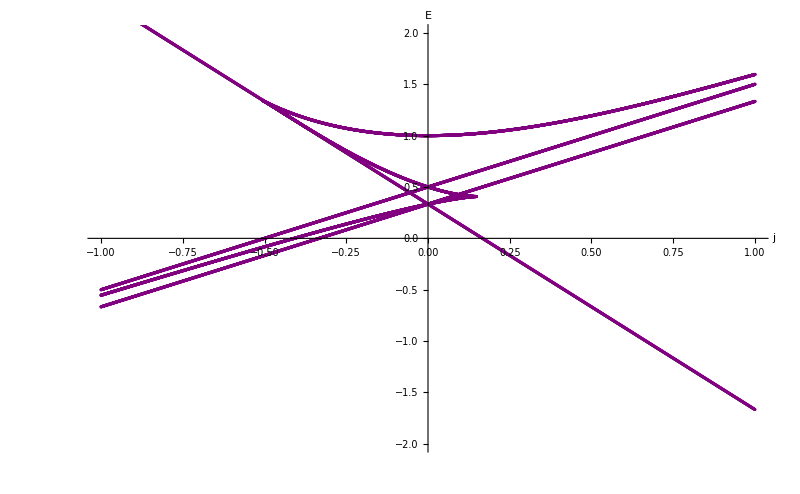

```mathematica
ListPlot[h,PlotRange->{-2,2},PlotStyle->Purple,AxesLabel->{"j","E"}]
```

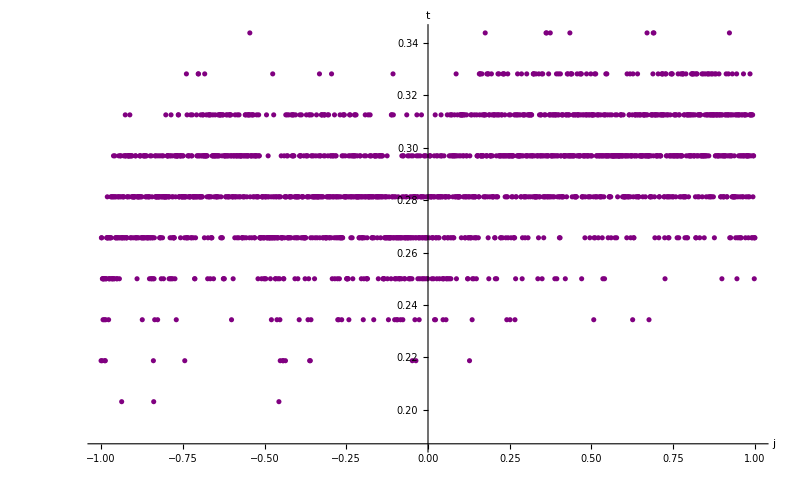

```mathematica
ListPlot[t,PlotStyle->Purple,AxesLabel->{"j","t"}]
```

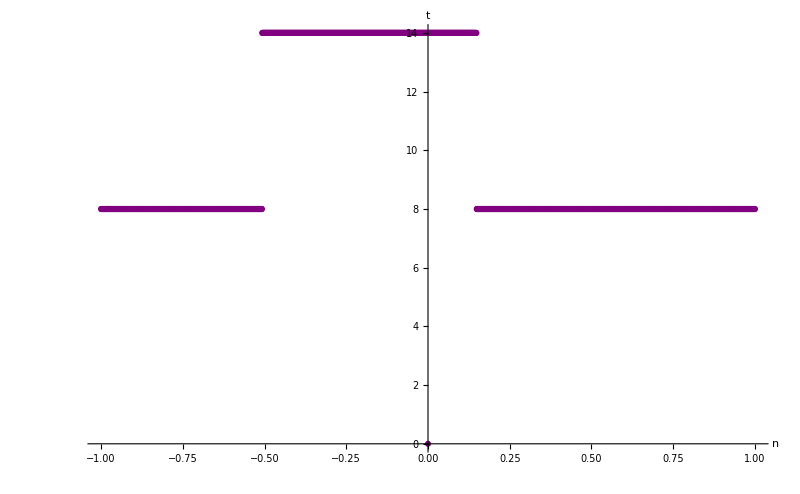

```mathematica
ListPlot[n,PlotStyle->Purple,AxesLabel->{"n","t"}]
```

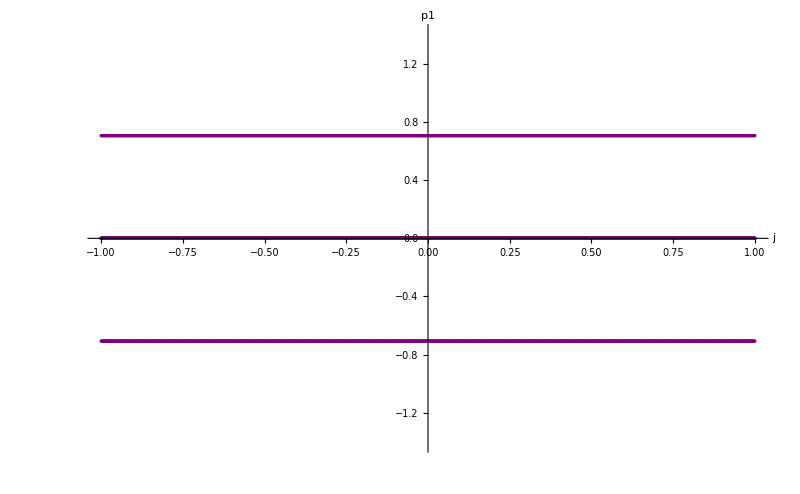

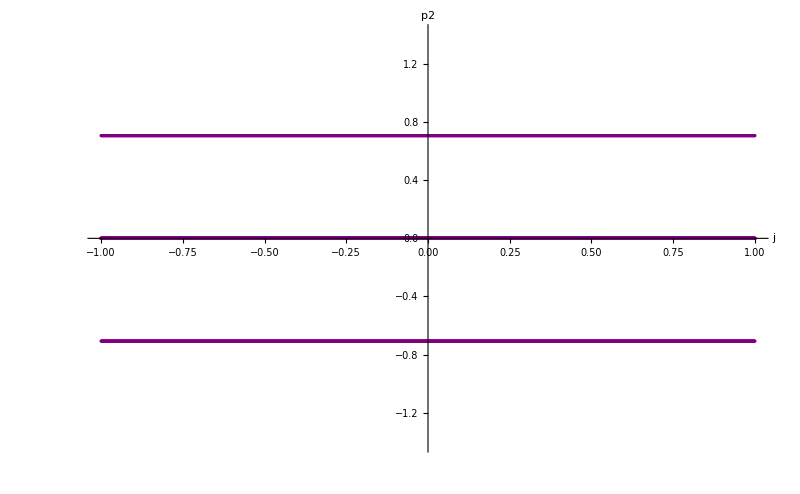

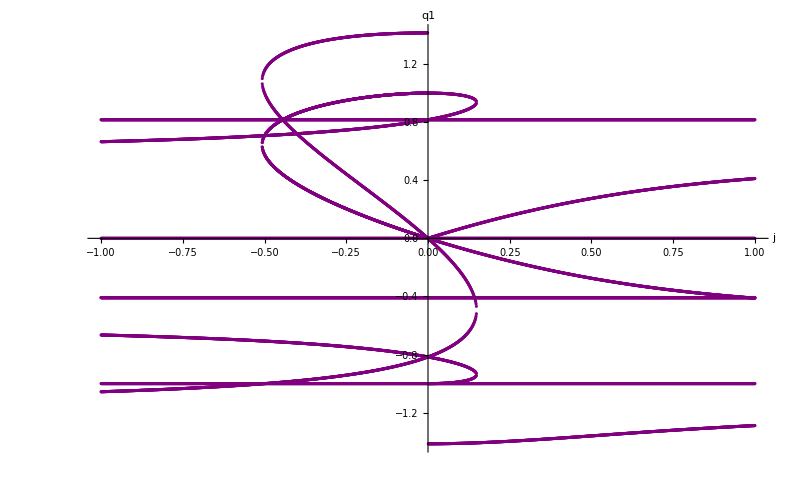

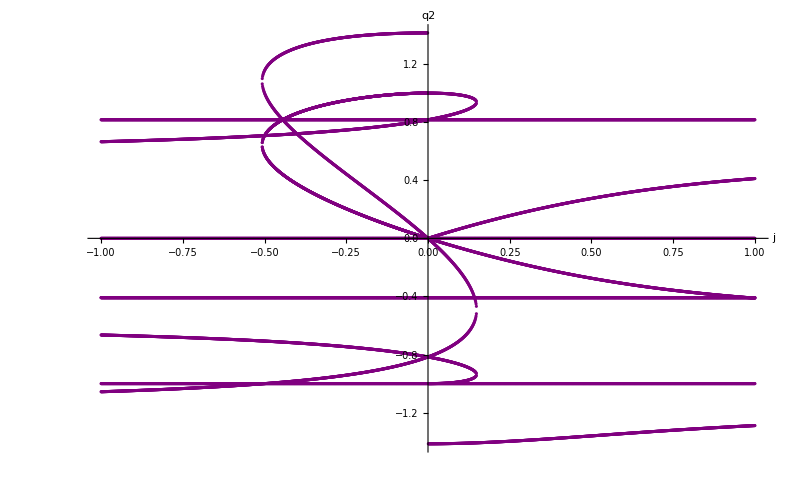

```mathematica
ListPlot[tp1,PlotRange->{-√2,√2},PlotStyle->Purple,AxesLabel->{"j","p1"}]
ListPlot[tp2,PlotRange->{-√2,√2},PlotStyle->Purple,AxesLabel->{"j","p2"}]
ListPlot[tq1,PlotRange->{-√2,√2},PlotStyle->Purple,AxesLabel->{"j","q1"}]
ListPlot[tq2,PlotRange->{-√2,√2},PlotStyle->Purple,AxesLabel->{"j","q2"}]
```

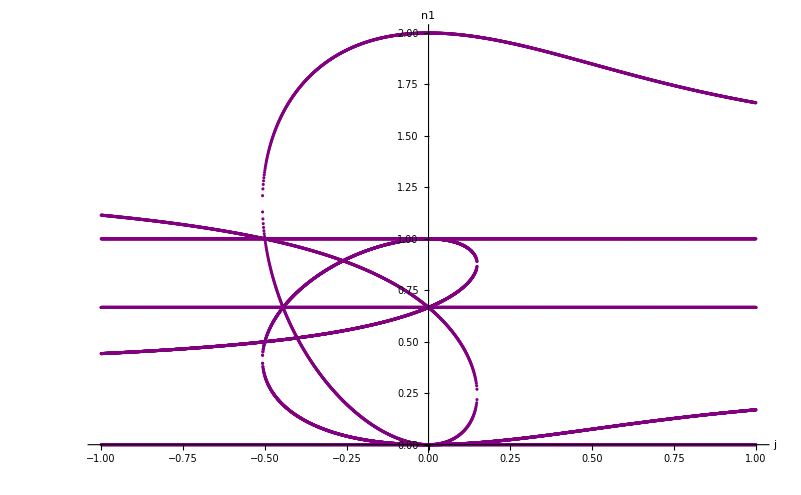

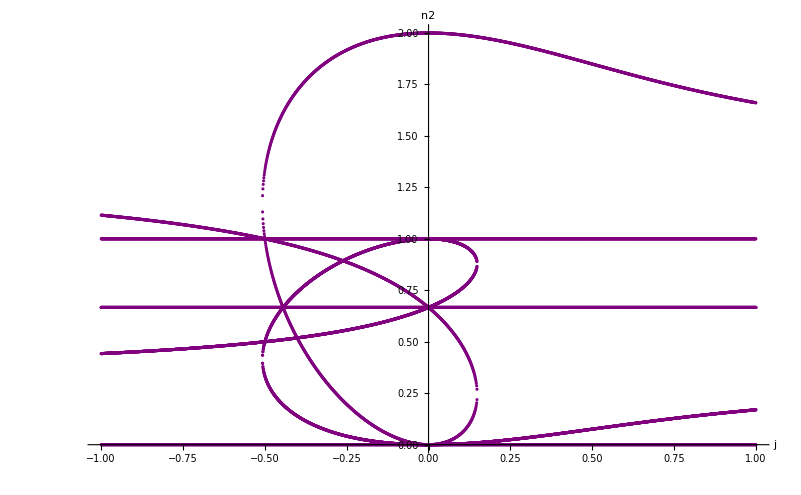

```mathematica
ListPlot[tn1,PlotRange->{0,2},PlotStyle->Purple,AxesLabel->{"j","n1"}]
ListPlot[tn2,PlotRange->{0,2},PlotStyle->Purple,AxesLabel->{"j","n2"}]
```

#### Saving

```mathematica
Export["d:\\h.txt",N[h],"CSV"];
Export["d:\\n.txt",N[n],"CSV"];
Export["d:\\t.txt",N[t],"CSV"];
Export["d:\\tq1.txt",N[tq1],"CSV"];
Export["d:\\tq2.txt",N[tq2],"CSV"];
Export["d:\\tq3.txt",N[tq3],"CSV"];
Export["d:\\tp1.txt",N[tp1],"CSV"];
Export["d:\\tp2.txt",N[tp2],"CSV"];
Export["d:\\tp3.txt",N[tp3],"CSV"];
```

### One-thread calculation

```mathematica
tq1={};
tq2={};
tq3={};
tp1={};
tp2={};
tp3={};

h={};
i={};
l={};
```

```mathematica
Monitor[For[j=j0,j≤2,j+=stepj,
t=Timing[TimeConstrained[s=Quiet[NSolve[{q1d==0,q2d==0,q3d=0,p1d==0,p2d==0,p3d==0},{q1,p1,q2,p2,q3,p3},Reals,WorkingPrecision->100]];
If[Length[s]>0,
h=Join[h,Tuples[{{j},hamiltonian[j,uu,p1,p2,p3,q1,q2,q3]/.s}]];
(*i=Join[i,Tuples[{{jj},(Total[Sign[Eigenvalues[#]]]/3-3)&/@(hessian[uu,jj]/.s)}]];*)
l=Join[l,{{ll,Length[s]}}];
tq1=Join[tq1,Tuples[{{j},q1/.s}]];
tq2=Join[tq2,Tuples[{{j},q2/.s}]];
tq3=Join[tq3,Tuples[{{j},q3/.s}]];
tp1=Join[tp1,Tuples[{{j},p1/.s}]];
tp2=Join[tp2,Tuples[{{j},p2/.s}]];
tp3=Join[tp3,Tuples[{{j},p3/.s}]]],300]][[1]]],{(j-j0)//N,t}];
```

$Aborted

### Full calculation

```mathematica
Monitor[For[c=c0,c≤1+c0,c+=stepc,
tx={};
ty={};
tpx={};
tpy={};
h={};
i={};
l={};
xd=FullSimplify[D[hamiltonian[AA,BB,c,px,py,x,y],px]];
yd=FullSimplify[D[hamiltonian[AA,BB,c,px,py,x,y],py]];
pxd=FullSimplify[D[hamiltonian[AA,BB,c,px,py,x,y],x]];
pyd=FullSimplify[D[hamiltonian[AA,BB,c,px,py,x,y],y]];
For[a=a0,a≤1,a+=stepa,
t=Timing[TimeConstrained[s=Quiet[Check[NSolve[{xd==0,yd==0,pxd==0,pyd==0}/.{AA->(1-a)/2,BB->-a},{x,px,y,py},Reals,WorkingPrecision->100],{}]];
If[Length[s]>0,
h=Join[h,Tuples[{{a},hamiltonian[(1-a)/2,-a,c,px,py,x,y]/.s}]];
i=Join[i,Tuples[{{a},(Total[Sign[Eigenvalues[#]]]/2-2)&/@(hessian[(1-a)/2,-a,c]/.s)}]];
l=Join[l,{{a,Length[s]}}];
tx=Join[tx,Tuples[{{a},x/.s}]];
ty=Join[ty,Tuples[{{a},y/.s}]];
tpx=Join[tpx,Tuples[{{a},px/.s}]];
tpy=Join[tpy,Tuples[{{a},py/.s}]]],60]][[1]]];
Export["D:\\results\\Vibron\\x" <> ToString[(c-c0)/stepc] <> ".png",ListPlot[tx,PlotRange->{-√2,√2},PlotStyle->Brown,PlotLabel->"C="<>ToString[N[c-c0,3]],AxesLabel->{"ξ","x"}]];
Export["D:\\results\\Vibron\\y" <> ToString[(c-c0)/stepc] <> ".png",ListPlot[ty,PlotRange->{-√2,√2},PlotLabel->"C="<>ToString[N[c-c0,3]],AxesLabel->{"ξ","y"}]];
Export["D:\\results\\Vibron\\px" <> ToString[(c-c0)/stepc] <> ".png",ListPlot[tpx,PlotRange->{-√2,√2},PlotStyle->Brown,PlotLabel->"C="<>ToString[N[c-c0,3]],AxesLabel->{"ξ","px"}]];
Export["D:\\results\\Vibron\\py" <> ToString[(c-c0)/stepc] <> ".png",ListPlot[tpy,PlotRange->{-√2,√2},PlotLabel->"C="<>ToString[N[c-c0,3]],AxesLabel->{"ξ","py"}]];
Export["D:\\results\\Vibron\\h" <> ToString[(c-c0)/stepc] <> ".png",ListPlot[h,PlotRange->{-2,2},PlotStyle->Purple,PlotLabel->"C="<>ToString[N[c-c0,3]],AxesLabel->{"ξ","E"}]]],{(a-a0)//N,(c-c0)//N,t}]
```